```mathematica
lst1={};
lst2={};
lst3={};
lst4={};
lst5={};
lst6={};
lst7={};
lst8={};
lst9={};
lst10={};
lst1 =Import["/home/san/Code/labs_comput/lab_5/res/1_4.txt","Table"]; 
lst2 =Import["/home/san/Code/labs_comput/lab_5/res/5_6.txt","Table"]; 
lst3 =Import["/home/san/Code/labs_comput/lab_5/res/7_8.txt","Table"]; 
lst4 =Import["/home/san/Code/labs_comput/lab_5/res/9_10.txt","Table"]; 
lst5 =Import["/home/san/Code/labs_comput/lab_5/res/11_12.txt","Table"]; 
lst6=Import["/home/san/Code/labs_comput/lab_5/res/13_15.txt","Table"]; 
lst7 =Import["/home/san/Code/labs_comput/lab_5/res/16_20.txt","Table"]; 
lst8 =Import["/home/san/Code/labs_comput/lab_5/res/21_25.txt","Table"];
lst9 =Import["/home/san/Code/labs_comput/lab_5/res/26_30.txt","Table"];
lst10 =Import["/home/san/Code/labs_comput/lab_5/res/30.txt","Table"];
```

```mathematica
lst1plt = ListPlot[lst1, PlotMarkers->{Black,Small}];
lst2plt = ListPlot[lst2,PlotMarkers->{Lighter[Black], ImageSize->Small},AspectRatio->1];
lst3plt = ListPlot[lst3, PlotMarkers->{Gray, ImageSize->Small}];
lst4plt = ListPlot[lst4, PlotMarkers->{Lighter[Gray], Small}];
lst5plt = ListPlot[lst5, PlotMarkers->{Yellow, Small}];
lst6plt = ListPlot[lst6, PlotStyle->{Black, Thickness[0.7]}];
{{lst7plt = ListPlot[lst7, PlotStyle->{Black, Thickness[0.7]}];}, {lst8plt = ListPlot[lst8, PlotStyle->{Black, Thickness[0.7]}];
lst9plt = ListPlot[lst9, PlotStyle->{Black, Thickness[0.7]}];
lst10plt = ListPlot[lst10, PlotMarkers->{White, Small}];}}
```

{{Null},{Null^3}}

```mathematica
ColorData[4,"ColorList"]
```

{RGBColor[0.2235294117647059, 0.2235294117647059, 0.2235294117647059],RGBColor[0.21176470588235294, 0.13725490196078433, 0.11372549019607843],RGBColor[0.5372549019607843, 0.3843137254901961, 0.2549019607843137],RGBColor[0.4235294117647059, 0.3254901960784314, 0.20784313725490197],RGBColor[0.9372549019607843, 0.7607843137254902, 0.403921568627451],RGBColor[0.996078431372549, 0.9058823529411765, 0.38823529411764707],RGBColor[0.6235294117647059, 0.592156862745098, 0.4],RGBColor[0.6980392156862745, 0.6745098039215687, 0.3686274509803922],RGBColor[0.41568627450980394, 0.45098039215686275, 0.3764705882352941],RGBColor[0.3333333333333333, 0.38823529411764707, 0.2901960784313726]}

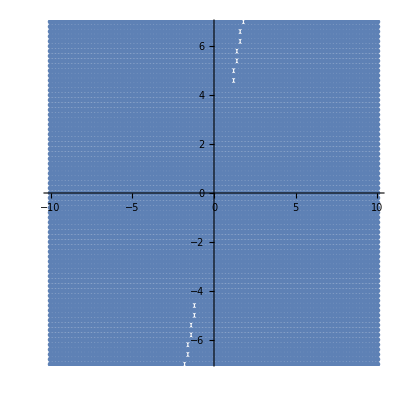

```mathematica
Show[ lst2plt,lst1plt,lst3plt,lst4plt,lst5plt, lst10plt]
```

```mathematica
Solve[{7*Sin[x]-4==0, 0<=x<=1}, x]//N
```

{{x→0.608246}}

```mathematica
1/((1 + Sqrt[5])/2)//N
```

0.618034